# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Klein-Nishina

Normalized variant of Klein-Nishina - energy parameter “e” = E_γ/(m_e c^2)

```mathematica
pKleinNishina[u_,e_]:=1/(1+e(1-u))1/((2 π Log[1+2 e])/e)
```

### Normalization condition

```mathematica
Integrate[2 Pi pKleinNishina[u,e],{u,-1,1},Assumptions->e>0]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pKleinNishina[u,e]u,{u,-1,1},Assumptions->e>0]
```

1+1/e-2/Log[1+2 e]

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->e>0]
```

1

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->e>0]
```

3+3/e-6/Log[1+2 e]

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->e>0]
```

5/4 (1+(3 (2+4 e+e^2-(4 e (1+e))/Log[1+2 e]))/e^2)

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->e>0]
```

(7 (15+45 e+36 e^2+6 e^3-(2 e (15+30 e+11 e^2))/Log[1+2 e]))/(6 e^3)

### sampling

```mathematica
cdf=Integrate[2 Pi pKleinNishina[u,e],{u,-1,x},Assumptions->e>0&&0<x<1]
```

1-Log[1+e-e x]/Log[1+2 e]

```mathematica
Solve[cdf==k,x]
```

{{x→ConditionalExpression[(1+e-(1+2 e)^(1-k))/e,-π≤Im[(-1+k) Log[1+2 e]]<π]}}

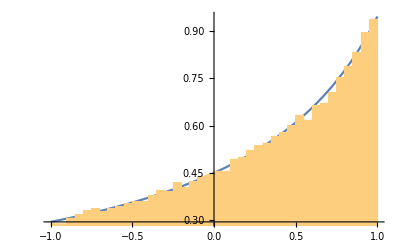

```mathematica
With[{e=1.1},

Show[
Plot[2 Pi pKleinNishina[u,e],{u,-1,1}],
Histogram[Map[(1+e-(1+2 e)^(1-#))/e&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
]
```